```mathematica
(*Mathematica*)
```

```mathematica
(* bezier Mandelbrot Julia: as a Julia set on complex plane c point*)
```

```mathematica
Clear[f,g0,g,v]
```

```mathematica
f[z_,i_]=z^2+(-0.019421134651027107+0.6406733898537237 ⅈ)*(i/30)+(1-i/30)*(0.14639804624826197+0.5819060009968053 ⅈ)
```

(0.146398+0.581906 ⅈ) (1-i/30)-(0.000647371-0.0213558 ⅈ) i+z^2

```mathematica
g1=Flatten[ParallelTable[{i,Timing[JuliaSetPlot[f[z,i],z,Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->{1920,1080},PlotStyle->{Opacity[0.2],Red,PointSize[0.0005]},AspectRatio->1,ImageResolution->1920,PerformanceGoal->"Quality","Bound"->32,Frame->False,Axes->False]][[1]]},{i,-3,2,6/100}]];
```

```mathematica
Length[g1]
```

168

```mathematica
g1
```

{-3,40.669,-147/50,38.8209,-72/25,39.6501,-141/50,42.5162,-69/25,41.0408,-27/10,39.2238,-66/25,39.9156,-129/50,38.9472,-63/25,38.3121,-123/50,41.2765,-12/5,37.2227,-117/50,37.1124,-57/25,40.5241,-111/50,39.7595,-54/25,42.7072,-21/10,39.9166,-51/25,41.1354,-99/50,42.4916,-48/25,42.0036,-93/50,39.5934,-9/5,41.4107,-87/50,40.5499,-42/25,42.1876,-81/50,39.8219,-39/25,39.1166,-3/2,41.7205,-36/25,38.906,-69/50,39.3607,-33/25,41.4663,-63/50,37.4861,-6/5,39.8911,-57/50,38.8033,-27/25,40.2759,-51/50,42.457,-24/25,38.5695,-9/10,39.8064,-21/25,39.2749,-39/50,38.3154,-18/25,37.5672,-33/50,37.9113,-3/5,38.0132,-27/50,37.1142,-12/25,37.1367,-21/50,35.4796,-9/25,37.0903,-3/10,43.8167,-6/25,39.0138,-9/50,40.9725,-3/25,36.7918,-3/50,39.864,0,44.2438,3/50,43.5581,3/25,42.6782,9/50,41.6166,6/25,42.9393,3/10,40.5827,9/25,40.0996,21/50,43.4872,12/25,41.4286,27/50,38.3323,3/5,42.8077,33/50,41.8324,18/25,43.8616,39/50,43.6346,21/25,42.3418,9/10,47.9643,24/25,43.8373,51/50,43.9298,27/25,38.4808,57/50,40.3028,6/5,35.9582,63/50,36.5506,33/25,37.3792,69/50,33.3326,36/25,33.907,3/2,40.63,39/25,39.2135,81/50,42.766,42/25,45.5954,87/50,41.6112,9/5,38.053,93/50,40.7683,48/25,36.504,99/50,33.9213}

```mathematica
gg=Table[N[{g1[[i]],g1[[i+1]]}],{i,1,Length[g1]-1,2}]
```

{{-3.,40.669},{-2.94,38.8209},{-2.88,39.6501},{-2.82,42.5162},{-2.76,41.0408},{-2.7,39.2238},{-2.64,39.9156},{-2.58,38.9472},{-2.52,38.3121},{-2.46,41.2765},{-2.4,37.2227},{-2.34,37.1124},{-2.28,40.5241},{-2.22,39.7595},{-2.16,42.7072},{-2.1,39.9166},{-2.04,41.1354},{-1.98,42.4916},{-1.92,42.0036},{-1.86,39.5934},{-1.8,41.4107},{-1.74,40.5499},{-1.68,42.1876},{-1.62,39.8219},{-1.56,39.1166},{-1.5,41.7205},{-1.44,38.906},{-1.38,39.3607},{-1.32,41.4663},{-1.26,37.4861},{-1.2,39.8911},{-1.14,38.8033},{-1.08,40.2759},{-1.02,42.457},{-0.96,38.5695},{-0.9,39.8064},{-0.84,39.2749},{-0.78,38.3154},{-0.72,37.5672},{-0.66,37.9113},{-0.6,38.0132},{-0.54,37.1142},{-0.48,37.1367},{-0.42,35.4796},{-0.36,37.0903},{-0.3,43.8167},{-0.24,39.0138},{-0.18,40.9725},{-0.12,36.7918},{-0.06,39.864},{0.,44.2438},{0.06,43.5581},{0.12,42.6782},{0.18,41.6166},{0.24,42.9393},{0.3,40.5827},{0.36,40.0996},{0.42,43.4872},{0.48,41.4286},{0.54,38.3323},{0.6,42.8077},{0.66,41.8324},{0.72,43.8616},{0.78,43.6346},{0.84,42.3418},{0.9,47.9643},{0.96,43.8373},{1.02,43.9298},{1.08,38.4808},{1.14,40.3028},{1.2,35.9582},{1.26,36.5506},{1.32,37.3792},{1.38,33.3326},{1.44,33.907},{1.5,40.63},{1.56,39.2135},{1.62,42.766},{1.68,45.5954},{1.74,41.6112},{1.8,38.053},{1.86,40.7683},{1.92,36.504},{1.98,33.9213}}

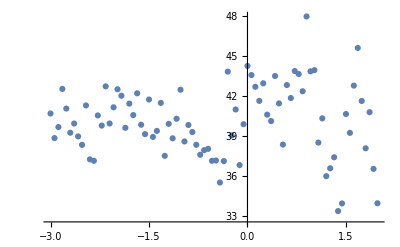

```mathematica
ListPlot[gg]
```

```mathematica
(*end*)
```